## First some formulae

```mathematica
Mult[x_]:=(3x+1)
```

```mathematica
MultSym[x_]:=(Style[3,Blue]x+Style[1,Red])
```

```mathematica
MyDiv [x_]:=x/2
```

```mathematica
MyDivSym [x_]:=x/Style[2,Darker[Green]]
```

```mathematica
MyPad[list_,n_]:=If[Length[list]<n,PadLeft[list,n],list]
```

```mathematica
ListToFunc[list_]:=Apply[Composition,Map[If[#==0,MyDiv,Mult]&,list]][x]
```

```mathematica
IntegerToList[n_]:=Apply[Composition,Map[If[#==0,MyDiv,Mult]&,Rest[IntegerDigits[n+2,2]]]][x]
```

```mathematica
FormatInteger[x_]:=If[IntegerQ[x]&&Positive[x],Framed[Style[x,18,Red],Background->LightYellow],x]
```

```mathematica
IntegerToListSym[n_]:=Apply[Composition,Map[If[#==0,MyDivSym,MultSym]&,Rest[IntegerDigits[n+2,2]]]][x]
```

```mathematica
ApplyOps[n_,ops_]:=Block[{result={},current=n,previousop=ops[[1]],pos},
Table[
previousop=op;
AppendTo[result,current];
If[op==0,current=current*2,current=(current -1)/3];
,{op,ops}];
result=Join[{n},result//Reverse];
For[pos=1,pos≤Length[ops],pos++,
result[[pos]]=Row[{result[[pos]],ops[[Length[ops]+1-pos]]/.{0->Style["↧",Red,Bold],1->Style["↥",Darker[Green],Bold]}}]
];
result[[Length[result]]]=FormatInteger[result[[Length[result]]]];
result
]
```

```mathematica
ApplyOpsGraph[n_,ops_]:=Block[{result={},current=n,previousop=ops[[1]]},
Table[
previousop=op;
AppendTo[result,current];
If[op==0,current=current*2,current=(current -1)/3];
,{op,ops}];
Append[Table[DirectedEdge[result[[k]],result[[k+1]],(ops[[k]]/.{1->Style["↧",Red,Bold],0->Style["↥",Darker[Green],Bold]})],{k,Length[result]-1}],
DirectedEdge[result[[Length[result]]],result[[1]],(ops[[Length[result]]]/.{1->Style["↧",Red,Bold],0->Style["↥",Darker[Green],Bold]})]
]
]
```

```mathematica
ApplyOpsGraph[n_,ops_]:=Block[{result={},current=n,previousop=ops[[1]]},
Table[
previousop=op;
AppendTo[result,current];
If[op==0,current=current*2,current=(current -1)/3];
,{op,ops}];
Append[Table[DirectedEdge[result[[k+1]],result[[k]]],{k,Length[result]-1}],
DirectedEdge[result[[1]],result[[Length[result]]]]
]
]
```

```mathematica
IntegerCycles[n_]:=Select[Range[n],With[{sol=(x/.First[Solve[IntegerToList[#]==x,x]])},IntegerQ[sol]&&Positive[sol]]&]
```

```mathematica
AnyIntegerCycles[n1_,n2_]:=Select[Range[n1,n2],With[{sol=(x/.First[Solve[IntegerToList[#]==x,x]])},IntegerQ[sol]]&]
```

## Now the calc

```mathematica
Map[Last,Table[{
{{k,
ApplyOpsGraph[(x/.First[Solve[IntegerToList[k]==x,x]]),Rest[IntegerDigits[k+2,2]]]}, {□}}},{k,
IntegerCycles[1000]}]]
```

Syntax::tsntxi: "k,ApplyOpsGraph[(x/.First[Solve[IntegerToList[k]==x,x]]),Rest[IntegerDigits[k+2,2]]]" is incomplete; more input is needed.

```mathematica
AnyIntegerCycles[-100,100]
```

{-87,-84,-75,-66,-58,-54,-52,-51,-46,-44,-43,-40,-39,-37,-34,-28,-23,-18,-14,-12,-11,-10,-8,-7,-6,-4,0,2,3,4,6,7,8,10,14,19,24,30,33,35,36,39,40,42,47,48,50,54,62,71,80,83,98}

```mathematica
FormatInteger[3]
```

3

```mathematica
ApplyOpsGraph[7,{0,1,1}]
```

{14->7,13/3->14,7->13/3}

```mathematica
IntegerCycles[30]
```

{7,8,10}

```mathematica
TableForm[Table[{
k,
Framed[Row[(Rest[IntegerDigits[k+2,2]]/.{0->Style["↧",Red,Bold],1->Style["↥",Darker[Green],Bold]})]],
(IntegerToList[k]//Factor//TraditionalForm),
(IntegerToListSym[k]//Factor//TraditionalForm),
Multicolumn[ApplyOps[Factor[(x/.First[Solve[IntegerToList[k]==x,x]])],Rest[IntegerDigits[k+2,2]]],Appearance -> "Horizontal"]
},{k,
IntegerCycles[20]}],TableHeadings->{None, {"k","ops","exp","long exp",   "cycle"}},
TableSpacing->{4, 1}, TableDepth->2]
```

k | ops | exp | long exp | cycle
7 | ↧↧↥ | 1/4 (3 x+1) | (3 x+1)/2^2 | 1↥ | 4↧
2↧ | 1
8 | ↧↥↧ | 1/4 (3 x+2) | (3 x+1 2)/2^2 | 2↧ | 1↥
4↧ | 2
10 | ↥↧↧ | 1/4 (3 x+4) | (3 x+1 2^2)/2^2 | 4↧ | 2↧
1↥ | 4

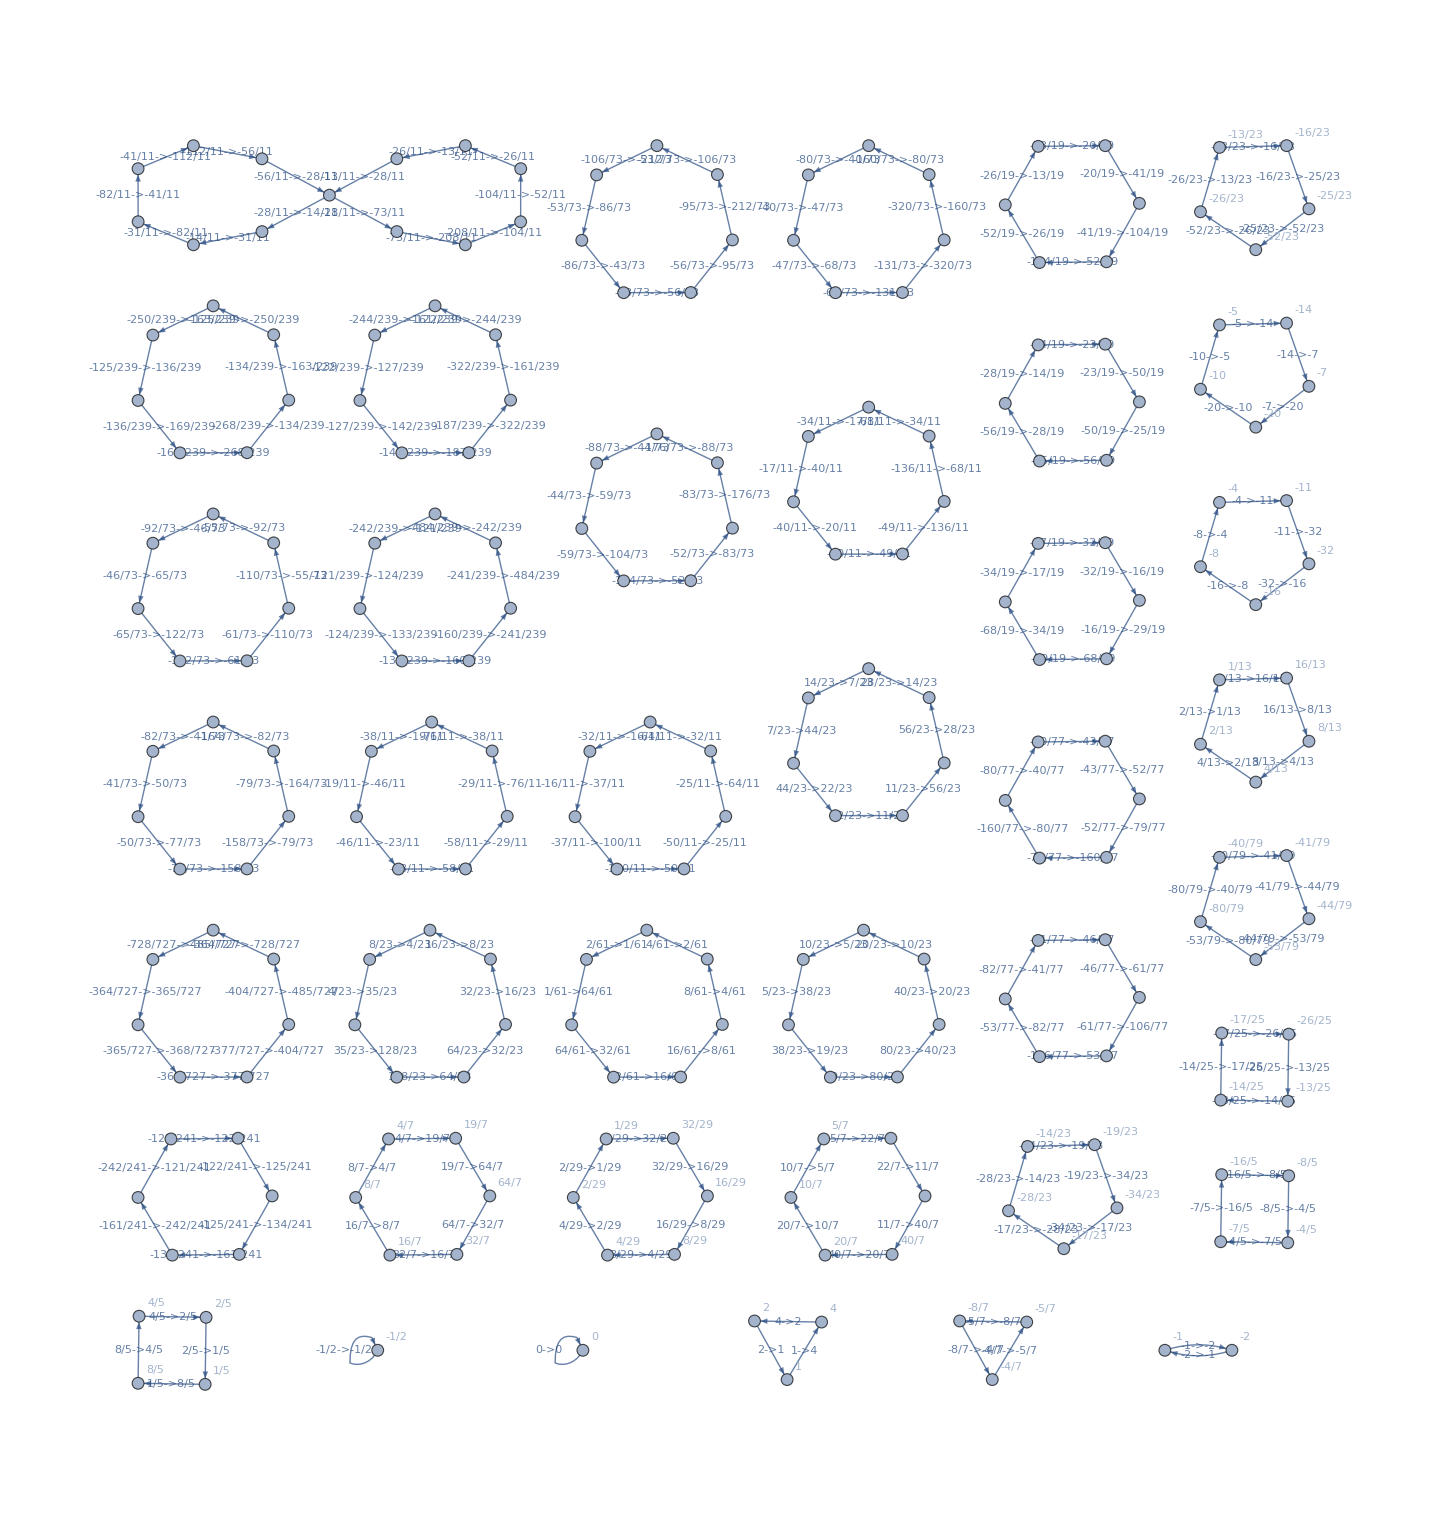

```mathematica
Graph[Flatten[Map[Last,Table[{
k,
ApplyOpsGraph[(x/.First[Solve[IntegerToList[k]==x,x]]),Rest[IntegerDigits[k+2,2]]]},{k,
200}]]]//DeleteDuplicates,VertexLabels->"Name", EdgeLabels->"Name"]
```

```mathematica
VertexLabels
```

```mathematica
With[{edges=Flatten[Map[Last,Table[{
k,
ApplyOpsGraph[(x/.First[Solve[IntegerToList[k]==x,x]]),Rest[IntegerDigits[k+2,2]]]},{k,
AnyIntegerCycles[1,10000000]}]]]//DeleteDuplicates},
Graph[edges,VertexLabels->"Name", EdgeStyle->Map[#->If[#[[1]]<#[[2]],Darker[Green],Red]&,edges]]
]
```

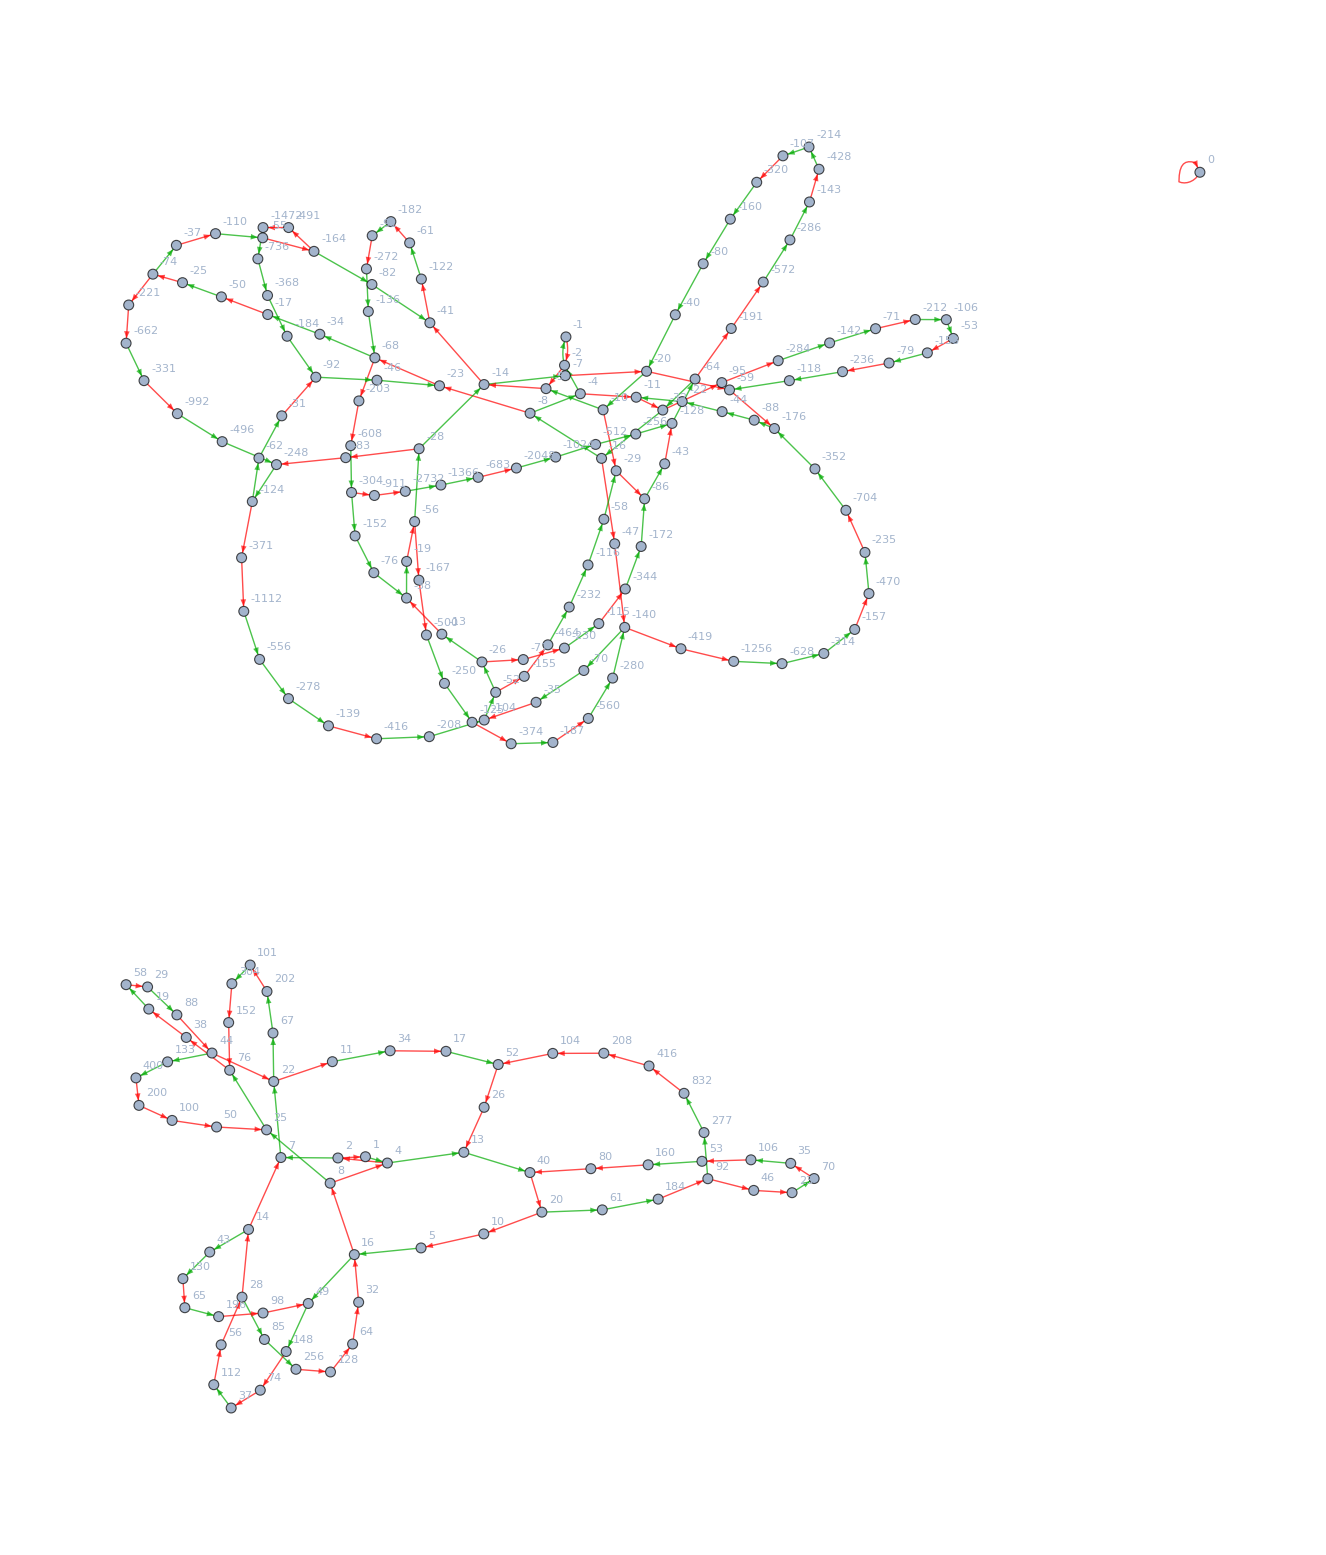

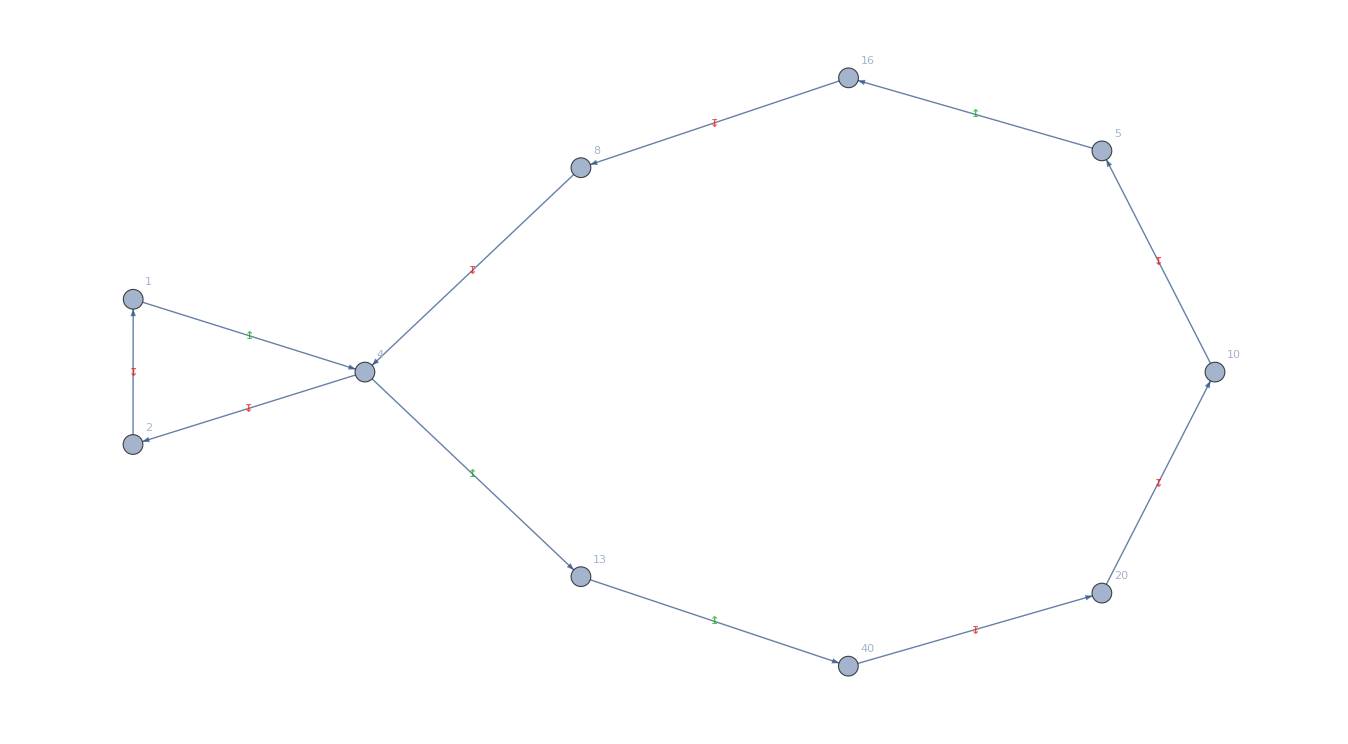

```mathematica
With[{edges=Flatten[Map[Last,Table[{
k,
ApplyOpsGraph[(x/.First[Solve[IntegerToList[k]==x,x]]),Rest[IntegerDigits[k+2,2]]]},{k,
IntegerCycles[1000]}]]]//DeleteDuplicates},
Graph[edges,VertexLabels->"Name", EdgeLabels->Map[#->If[#[[1]]<#[[2]],Style["↥",Darker[Green],Bold],Style["↧",Red,Bold]]&,edges]]
]
```

```mathematica
TableForm[DeleteDuplicates[Table[With[{
sol=(x/.First[Solve[IntegerToList[k]==x,x]])},{
sol,
k,
Framed[Row[(Rest[IntegerDigits[k+2,2]]/.{0->Style["↧",Red,Bold],1->Style["↥",Darker[Green],Bold]})//Reverse]],
(IntegerToList[k]//Factor//TraditionalForm),
(IntegerToListSym[k]//Factor//TraditionalForm),
Multicolumn[ApplyOps[Factor[(x/.First[Solve[IntegerToList[k]==x,x]])],Rest[IntegerDigits[k+2,2]]],Appearance -> "Horizontal"]
}
],{k,IntegerCycles[20000]}],#1[[1]]==#2[[1]]&],TableHeadings->{None, {"k","ops","exp","long exp",   "cycle"}},
TableSpacing->{4, 1}, TableDepth->2]
```

k | ops | exp | long exp | cycle | 
1 | 7 | ↥↧↧ | 1/4 (3 x+1) | (3 x+1)/2^2 | 1↥ | 4↧
2↧ | 1
2 | 8 | ↧↥↧ | 1/4 (3 x+2) | (3 x+1 2)/2^2 | 2↧ | 1↥
4↧ | 2
4 | 10 | ↧↧↥ | 1/4 (3 x+4) | (3 x+1 2^2)/2^2 | 4↧ | 2↧
1↥ | 4
5 | 279 | ↥↧↧↥↥↧↧↧ | 1/32 (27 x+25) | (3^3 x+1 3^2+1 2^2 3+1 2^2)/2^5 | 5↥ | 16↧ | 8↧
4↥ | 13↥ | 40↧
20↧ | 10↧ | 5
10 | 304 | ↧↥↧↧↥↥↧↧ | 1/32 (27 x+50) | (3^3 x+1 2^3+1 3 2^3+1 3^2 2)/2^5 | 10↧ | 5↥ | 16↧
8↧ | 4↥ | 13↥
40↧ | 20↧ | 10
8 | 324 | ↧↥↥↧↧↧↥↧ | 1/32 (27 x+40) | (3^3 x+1 2^4+1 3^2 2+1 3 2)/2^5 | 8↧ | 4↥ | 13↥
40↧ | 20↧ | 10↧
5↥ | 16↧ | 8
20 | 354 | ↧↧↥↧↧↥↥↧ | 1/32 (27 x+100) | (3^3 x+1 2^4+1 3 2^4+1 3^2 2^2)/2^5 | 20↧ | 10↧ | 5↥
16↧ | 8↧ | 4↥
13↥ | 40↧ | 20
16 | 394 | ↧↧↥↥↧↧↧↥ | 1/32 (27 x+80) | (3^3 x+1 2^5+1 3^2 2^2+1 3 2^2)/2^5 | 16↧ | 8↧ | 4↥
13↥ | 40↧ | 20↧
10↧ | 5↥ | 16
13 | 399 | ↥↧↧↧↥↧↧↥ | 1/32 (27 x+65) | (3^3 x+1 2^5+1 3 2^3+1 3^2)/2^5 | 13↥ | 40↧ | 20↧
10↧ | 5↥ | 16↧
8↧ | 4↥ | 13
40 | 454 | ↧↧↧↥↧↧↥↥ | 1/32 (27 x+200) | (3^3 x+1 2^5+1 3 2^5+1 3^2 2^3)/2^5 | 40↧ | 20↧ | 10↧
5↥ | 16↧ | 8↧
4↥ | 13↥ | 40
26 | 8408 | ↧↥↧↥↥↧↥↥↧↧↧↧↧ | 1/256 (243 x+338) | (3^5 x+1 2 3^4+1 2^2 3^3+1 2^2 3^2+1 2^3 3+1 2^3)/2^8 | 26↧ | 13↥ | 40↧ | 20↥
61↥ | 184↧ | 92↥ | 277↥
832↧ | 416↧ | 208↧ | 104↧
52↧ | 26 |  | 
19 | 8547 | ↥↧↥↧↧↥↥↧↥↧↧↧↧ | 1/256 (243 x+247) | (3^5 x+1 3^4+1 2 3^3+1 2^3 3^2+1 2^3 3+1 2^4)/2^8 | 19↥ | 58↧ | 29↥ | 88↧
44↧ | 22↥ | 67↥ | 202↧
101↥ | 304↧ | 152↧ | 76↧
38↧ | 19 |  | 
25 | 8615 | ↥↧↧↥↧↥↧↥↥↧↧↧↧ | 1/256 (243 x+325) | (3^5 x+1 3^4+1 2^2 3^3+1 2^3 3^2+1 2^4 3+1 2^4)/2^8 | 25↥ | 76↧ | 38↧ | 19↥
58↧ | 29↥ | 88↧ | 44↥
133↥ | 400↧ | 200↧ | 100↧
50↧ | 25 |  | 
52 | 8626 | ↧↧↥↧↥↥↧↥↥↧↧↧↧ | 1/256 (243 x+676) | (3^5 x+1 2^2 3^4+1 2^3 3^3+1 2^3 3^2+1 2^4 3+1 2^4)/2^8 | 52↧ | 26↧ | 13↥ | 40↧
20↥ | 61↥ | 184↧ | 92↥
277↥ | 832↧ | 416↧ | 208↧
104↧ | 52 |  | 
14 | 8777 | ↥↥↧↥↧↧↥↧↧↥↧↧↧ | 1/256 (243 x+182) | (3^5 x+1 2^5+1 3 2^3+1 3^2 2+1 3^4+1 3^3)/2^8 | 14↥ | 43↥ | 130↧ | 65↥
196↧ | 98↧ | 49↥ | 148↧
74↧ | 37↥ | 112↧ | 56↧
28↧ | 14 |  | 
38 | 8904 | ↧↥↧↥↧↧↥↥↧↥↧↧↧ | 1/256 (243 x+494) | (3^5 x+1 2^5+1 3^2 2^4+1 3 2^4+1 3^3 2^2+1 3^4 2)/2^8 | 38↧ | 19↥ | 58↧ | 29↥
88↧ | 44↧ | 22↥ | 67↥
202↧ | 101↥ | 304↧ | 152↧
76↧ | 38 |  | 
23 | 8979 | ↥↧↥↧↥↧↧↧↥↥↧↧↧ | 1/256 (243 x+299) | (3^5 x+1 2^5+1 3 2^5+1 3^2 2^2+1 3^3 2+1 3^4)/2^8 | 23↥ | 70↧ | 35↥ | 106↧
53↥ | 160↧ | 80↧ | 40↧
20↥ | 61↥ | 184↧ | 92↧
46↧ | 23 |  | 
32 | 8996 | ↧↥↥↧↧↥↧↧↥↥↧↧↧ | 1/256 (243 x+416) | (3^5 x+1 2^5+1 3 2^5+1 3^2 2^3+1 3^4 2+1 3^3 2)/2^8 | 32↧ | 16↥ | 49↥ | 148↧
74↧ | 37↥ | 112↧ | 56↧
28↥ | 85↥ | 256↧ | 128↧
64↧ | 32 |  | 
50 | 9040 | ↧↥↧↧↥↧↥↧↥↥↧↧↧ | 1/256 (243 x+650) | (3^5 x+1 2^5+1 3 2^5+1 3^2 2^4+1 3^3 2^3+1 3^4 2)/2^8 | 50↧ | 25↥ | 76↧ | 38↧
19↥ | 58↧ | 29↥ | 88↧
44↥ | 133↥ | 400↧ | 200↧
100↧ | 50 |  | 
104 | 9062 | ↧↧↧↥↧↥↥↧↥↥↧↧↧ | 1/256 (243 x+1352) | (3^5 x+1 2^5+1 3 2^5+1 3^3 2^4+1 3^2 2^4+1 3^4 2^3)/2^8 | 104↧ | 52↧ | 26↧ | 13↥
40↧ | 20↥ | 61↥ | 184↧
92↥ | 277↥ | 832↧ | 416↧
208↧ | 104 |  | 
28 | 9364 | ↧↥↥↧↥↧↧↥↧↧↥↧↧ | 1/256 (243 x+364) | (3^5 x+1 2^6+1 3 2^4+1 3^2 2^2+1 3^4 2+1 3^3 2)/2^8 | 28↧ | 14↥ | 43↥ | 130↧
65↥ | 196↧ | 98↧ | 49↥
148↧ | 74↧ | 37↥ | 112↧
56↧ | 28 |  | 
37 | 9391 | ↥↧↧↧↥↥↧↥↧↧↥↧↧ | 1/256 (243 x+481) | (3^5 x+1 2^6+1 3 2^4+1 3^3 2^3+1 3^2 2^3+1 3^4)/2^8 | 37↥ | 112↧ | 56↧ | 28↧
14↥ | 43↥ | 130↧ | 65↥
196↧ | 98↧ | 49↥ | 148↧
74↧ | 37 |  | 
22 | 9481 | ↥↥↧↥↧↧↧↧↥↧↥↧↧ | 1/256 (243 x+286) | (3^5 x+1 2^6+1 3 2^5+1 3^2 2+1 3^4+1 3^3)/2^8 | 22↥ | 67↥ | 202↧ | 101↥
304↧ | 152↧ | 76↧ | 38↧
19↥ | 58↧ | 29↥ | 88↧
44↧ | 22 |  | 
49 | 9607 | ↥↧↧↥↧↧↧↥↥↧↥↧↧ | 1/256 (243 x+637) | (3^5 x+1 2^6+1 3^2 2^5+1 3 2^5+1 3^3 2^2+1 3^4)/2^8 | 49↥ | 148↧ | 74↧ | 37↥
112↧ | 56↧ | 28↧ | 14↥
43↥ | 130↧ | 65↥ | 196↧
98↧ | 49 |  | 
76 | 9618 | ↧↧↥↧↥↧↧↥↥↧↥↧↧ | 1/256 (243 x+988) | (3^5 x+1 2^6+1 3^2 2^5+1 3 2^5+1 3^3 2^3+1 3^4 2^2)/2^8 | 76↧ | 38↧ | 19↥ | 58↧
29↥ | 88↧ | 44↧ | 22↥
67↥ | 202↧ | 101↥ | 304↧
152↧ | 76 |  | 
46 | 9768 | ↧↥↧↥↧↥↧↧↧↥↥↧↧ | 1/256 (243 x+598) | (3^5 x+1 2^6+1 3 2^6+1 3^2 2^3+1 3^3 2^2+1 3^4 2)/2^8 | 46↧ | 23↥ | 70↧ | 35↥
106↧ | 53↥ | 160↧ | 80↧
40↧ | 20↥ | 61↥ | 184↧
92↧ | 46 |  | 
64 | 9802 | ↧↧↥↥↧↧↥↧↧↥↥↧↧ | 1/256 (243 x+832) | (3^5 x+1 2^6+1 3 2^6+1 3^2 2^4+1 3^4 2^2+1 3^3 2^2)/2^8 | 64↧ | 32↧ | 16↥ | 49↥
148↧ | 74↧ | 37↥ | 112↧
56↧ | 28↥ | 85↥ | 256↧
128↧ | 64 |  | 
100 | 9890 | ↧↧↥↧↧↥↧↥↧↥↥↧↧ | 1/256 (243 x+1300) | (3^5 x+1 2^6+1 3 2^6+1 3^2 2^5+1 3^3 2^4+1 3^4 2^2)/2^8 | 100↧ | 50↧ | 25↥ | 76↧
38↧ | 19↥ | 58↧ | 29↥
88↧ | 44↥ | 133↥ | 400↧
200↧ | 100 |  | 
208 | 9934 | ↧↧↧↧↥↧↥↥↧↥↥↧↧ | 1/256 (243 x+2704) | (3^5 x+1 2^6+1 3 2^6+1 3^3 2^5+1 3^2 2^5+1 3^4 2^4)/2^8 | 208↧ | 104↧ | 52↧ | 26↧
13↥ | 40↧ | 20↥ | 61↥
184↧ | 92↥ | 277↥ | 832↧
416↧ | 208 |  | 
29 | 10327 | ↥↧↧↥↥↧↥↧↧↧↧↥↧ | 1/256 (243 x+377) | (3^5 x+1 2^7+1 3 2^3+1 3^3 2^2+1 3^2 2^2+1 3^4)/2^8 | 29↥ | 88↧ | 44↧ | 22↥
67↥ | 202↧ | 101↥ | 304↧
152↧ | 76↧ | 38↧ | 19↥
58↧ | 29 |  | 
35 | 10435 | ↥↧↥↧↧↧↥↥↧↧↧↥↧ | 1/256 (243 x+455) | (3^5 x+1 2^7+1 3^2 2^4+1 3 2^4+1 3^3 2+1 3^4)/2^8 | 35↥ | 106↧ | 53↥ | 160↧
80↧ | 40↧ | 20↥ | 61↥
184↧ | 92↧ | 46↧ | 23↥
70↧ | 35 |  | 
56 | 10538 | ↧↧↥↥↧↥↧↧↥↧↧↥↧ | 1/256 (243 x+728) | (3^5 x+1 2^7+1 3 2^5+1 3^2 2^3+1 3^4 2^2+1 3^3 2^2)/2^8 | 56↧ | 28↧ | 14↥ | 43↥
130↧ | 65↥ | 196↧ | 98↧
49↥ | 148↧ | 74↧ | 37↥
112↧ | 56 |  | 
74 | 10592 | ↧↥↧↧↧↥↥↧↥↧↧↥↧ | 1/256 (243 x+962) | (3^5 x+1 2^7+1 3 2^5+1 3^3 2^4+1 3^2 2^4+1 3^4 2)/2^8 | 74↧ | 37↥ | 112↧ | 56↧
28↧ | 14↥ | 43↥ | 130↧
65↥ | 196↧ | 98↧ | 49↥
148↧ | 74 |  | 
44 | 10772 | ↧↥↥↧↥↧↧↧↧↥↧↥↧ | 1/256 (243 x+572) | (3^5 x+1 2^7+1 3 2^6+1 3^2 2^2+1 3^4 2+1 3^3 2)/2^8 | 44↧ | 22↥ | 67↥ | 202↧
101↥ | 304↧ | 152↧ | 76↧
38↧ | 19↥ | 58↧ | 29↥
88↧ | 44 |  | 
53 | 10799 | ↥↧↧↧↥↥↧↧↧↥↧↥↧ | 1/256 (243 x+689) | (3^5 x+1 2^7+1 3 2^6+1 3^3 2^3+1 3^2 2^3+1 3^4)/2^8 | 53↥ | 160↧ | 80↧ | 40↧
20↥ | 61↥ | 184↧ | 92↧
46↧ | 23↥ | 70↧ | 35↥
106↧ | 53 |  | 
80 | 10890 | ↧↧↥↥↧↧↧↥↧↥↧↥↧ | 1/256 (243 x+1040) | (3^5 x+1 2^7+1 3 2^6+1 3^2 2^5+1 3^4 2^2+1 3^3 2^2)/2^8 | 80↧ | 40↧ | 20↥ | 61↥
184↧ | 92↧ | 46↧ | 23↥
70↧ | 35↥ | 106↧ | 53↥
160↧ | 80 |  | 
98 | 11024 | ↧↥↧↧↥↧↧↧↥↥↧↥↧ | 1/256 (243 x+1274) | (3^5 x+1 2^7+1 3^2 2^6+1 3 2^6+1 3^3 2^3+1 3^4 2)/2^8 | 98↧ | 49↥ | 148↧ | 74↧
37↥ | 112↧ | 56↧ | 28↧
14↥ | 43↥ | 130↧ | 65↥
196↧ | 98 |  | 
152 | 11046 | ↧↧↧↥↧↥↧↧↥↥↧↥↧ | 1/256 (243 x+1976) | (3^5 x+1 2^7+1 3^2 2^6+1 3 2^6+1 3^3 2^4+1 3^4 2^3)/2^8 | 152↧ | 76↧ | 38↧ | 19↥
58↧ | 29↥ | 88↧ | 44↧
22↥ | 67↥ | 202↧ | 101↥
304↧ | 152 |  | 
65 | 11335 | ↥↧↧↥↧↧↥↧↧↧↥↥↧ | 1/256 (243 x+845) | (3^5 x+1 2^7+1 3 2^7+1 3^2 2^4+1 3^3 2^2+1 3^4)/2^8 | 65↥ | 196↧ | 98↧ | 49↥
148↧ | 74↧ | 37↥ | 112↧
56↧ | 28↧ | 14↥ | 43↥
130↧ | 65 |  | 
92 | 11346 | ↧↧↥↧↥↧↥↧↧↧↥↥↧ | 1/256 (243 x+1196) | (3^5 x+1 2^7+1 3 2^7+1 3^2 2^4+1 3^3 2^3+1 3^4 2^2)/2^8 | 92↧ | 46↧ | 23↥ | 70↧
35↥ | 106↧ | 53↥ | 160↧
80↧ | 40↧ | 20↥ | 61↥
184↧ | 92 |  | 
128 | 11414 | ↧↧↧↥↥↧↧↥↧↧↥↥↧ | 1/256 (243 x+1664) | (3^5 x+1 2^7+1 3 2^7+1 3^2 2^5+1 3^4 2^3+1 3^3 2^3)/2^8 | 128↧ | 64↧ | 32↧ | 16↥
49↥ | 148↧ | 74↧ | 37↥
112↧ | 56↧ | 28↥ | 85↥
256↧ | 128 |  | 
101 | 11423 | ↥↧↧↧↧↥↧↥↧↧↥↥↧ | 1/256 (243 x+1313) | (3^5 x+1 2^7+1 3 2^7+1 3^2 2^5+1 3^3 2^4+1 3^4)/2^8 | 101↥ | 304↧ | 152↧ | 76↧
38↧ | 19↥ | 58↧ | 29↥
88↧ | 44↧ | 22↥ | 67↥
202↧ | 101 |  | 
200 | 11590 | ↧↧↧↥↧↧↥↧↥↧↥↥↧ | 1/256 (243 x+2600) | (3^5 x+1 2^7+1 3 2^7+1 3^2 2^6+1 3^3 2^5+1 3^4 2^3)/2^8 | 200↧ | 100↧ | 50↧ | 25↥
76↧ | 38↧ | 19↥ | 58↧
29↥ | 88↧ | 44↥ | 133↥
400↧ | 200 |  | 
416 | 11678 | ↧↧↧↧↧↥↧↥↥↧↥↥↧ | 1/256 (243 x+5408) | (3^5 x+1 2^7+1 3 2^7+1 3^3 2^6+1 3^2 2^6+1 3^4 2^5)/2^8 | 416↧ | 208↧ | 104↧ | 52↧
26↧ | 13↥ | 40↧ | 20↥
61↥ | 184↧ | 92↥ | 277↥
832↧ | 416 |  | 
58 | 12464 | ↧↥↧↧↥↥↧↥↧↧↧↧↥ | 1/256 (243 x+754) | (3^5 x+1 2^8+1 3 2^4+1 3^3 2^3+1 3^2 2^3+1 3^4 2)/2^8 | 58↧ | 29↥ | 88↧ | 44↧
22↥ | 67↥ | 202↧ | 101↥
304↧ | 152↧ | 76↧ | 38↧
19↥ | 58 |  | 
43 | 12579 | ↥↧↥↧↧↥↧↧↥↧↧↧↥ | 1/256 (243 x+559) | (3^5 x+1 2^8+1 3 2^5+1 3^2 2^3+1 3^3 2+1 3^4)/2^8 | 43↥ | 130↧ | 65↥ | 196↧
98↧ | 49↥ | 148↧ | 74↧
37↥ | 112↧ | 56↧ | 28↧
14↥ | 43 |  | 
61 | 12623 | ↥↧↧↧↥↧↥↧↥↧↧↧↥ | 1/256 (243 x+793) | (3^5 x+1 2^8+1 3 2^5+1 3^2 2^4+1 3^3 2^3+1 3^4)/2^8 | 61↥ | 184↧ | 92↧ | 46↧
23↥ | 70↧ | 35↥ | 106↧
53↥ | 160↧ | 80↧ | 40↧
20↥ | 61 |  | 
70 | 12680 | ↧↥↧↥↧↧↧↥↥↧↧↧↥ | 1/256 (243 x+910) | (3^5 x+1 2^8+1 3^2 2^5+1 3 2^5+1 3^3 2^2+1 3^4 2)/2^8 | 70↧ | 35↥ | 106↧ | 53↥
160↧ | 80↧ | 40↧ | 20↥
61↥ | 184↧ | 92↧ | 46↧
23↥ | 70 |  | 
112 | 12886 | ↧↧↧↥↥↧↥↧↧↥↧↧↥ | 1/256 (243 x+1456) | (3^5 x+1 2^8+1 3 2^6+1 3^2 2^4+1 3^4 2^3+1 3^3 2^3)/2^8 | 112↧ | 56↧ | 28↧ | 14↥
43↥ | 130↧ | 65↥ | 196↧
98↧ | 49↥ | 148↧ | 74↧
37↥ | 112 |  | 
85 | 12895 | ↥↧↧↧↧↥↥↧↧↥↧↧↥ | 1/256 (243 x+1105) | (3^5 x+1 2^8+1 3 2^6+1 3^3 2^4+1 3^2 2^4+1 3^4)/2^8 | 85↥ | 256↧ | 128↧ | 64↧
32↧ | 16↥ | 49↥ | 148↧
74↧ | 37↥ | 112↧ | 56↧
28↥ | 85 |  | 
67 | 12931 | ↥↧↥↧↧↧↧↥↧↥↧↧↥ | 1/256 (243 x+871) | (3^5 x+1 2^8+1 3 2^6+1 3^2 2^5+1 3^3 2+1 3^4)/2^8 | 67↥ | 202↧ | 101↥ | 304↧
152↧ | 76↧ | 38↧ | 19↥
58↧ | 29↥ | 88↧ | 44↧
22↥ | 67 |  | 
148 | 12994 | ↧↧↥↧↧↧↥↥↧↥↧↧↥ | 1/256 (243 x+1924) | (3^5 x+1 2^8+1 3 2^6+1 3^3 2^5+1 3^2 2^5+1 3^4 2^2)/2^8 | 148↧ | 74↧ | 37↥ | 112↧
56↧ | 28↧ | 14↥ | 43↥
130↧ | 65↥ | 196↧ | 98↧
49↥ | 148 |  | 
88 | 13354 | ↧↧↥↥↧↥↧↧↧↧↥↧↥ | 1/256 (243 x+1144) | (3^5 x+1 2^8+1 3 2^7+1 3^2 2^3+1 3^4 2^2+1 3^3 2^2)/2^8 | 88↧ | 44↧ | 22↥ | 67↥
202↧ | 101↥ | 304↧ | 152↧
76↧ | 38↧ | 19↥ | 58↧
29↥ | 88 |  | 
106 | 13408 | ↧↥↧↧↧↥↥↧↧↧↥↧↥ | 1/256 (243 x+1378) | (3^5 x+1 2^8+1 3 2^7+1 3^3 2^4+1 3^2 2^4+1 3^4 2)/2^8 | 106↧ | 53↥ | 160↧ | 80↧
40↧ | 20↥ | 61↥ | 184↧
92↧ | 46↧ | 23↥ | 70↧
35↥ | 106 |  | 
160 | 13590 | ↧↧↧↥↥↧↧↧↥↧↥↧↥ | 1/256 (243 x+2080) | (3^5 x+1 2^8+1 3 2^7+1 3^2 2^6+1 3^4 2^3+1 3^3 2^3)/2^8 | 160↧ | 80↧ | 40↧ | 20↥
61↥ | 184↧ | 92↧ | 46↧
23↥ | 70↧ | 35↥ | 106↧
53↥ | 160 |  | 
133 | 13599 | ↥↧↧↧↧↥↧↧↥↧↥↧↥ | 1/256 (243 x+1729) | (3^5 x+1 2^8+1 3 2^7+1 3^2 2^6+1 3^3 2^4+1 3^4)/2^8 | 133↥ | 400↧ | 200↧ | 100↧
50↧ | 25↥ | 76↧ | 38↧
19↥ | 58↧ | 29↥ | 88↧
44↥ | 133 |  | 
196 | 13858 | ↧↧↥↧↧↥↧↧↧↥↥↧↥ | 1/256 (243 x+2548) | (3^5 x+1 2^8+1 3^2 2^7+1 3 2^7+1 3^3 2^4+1 3^4 2^2)/2^8 | 196↧ | 98↧ | 49↥ | 148↧
74↧ | 37↥ | 112↧ | 56↧
28↧ | 14↥ | 43↥ | 130↧
65↥ | 196 |  | 
304 | 13902 | ↧↧↧↧↥↧↥↧↧↥↥↧↥ | 1/256 (243 x+3952) | (3^5 x+1 2^8+1 3^2 2^7+1 3 2^7+1 3^3 2^5+1 3^4 2^4)/2^8 | 304↧ | 152↧ | 76↧ | 38↧
19↥ | 58↧ | 29↥ | 88↧
44↧ | 22↥ | 67↥ | 202↧
101↥ | 304 |  | 
277 | 13951 | ↥↧↧↧↧↧↧↥↧↥↥↧↥ | 1/256 (243 x+3601) | (3^5 x+1 2^8+1 3^2 2^7+1 3 2^7+1 3^3 2^6+1 3^4)/2^8 | 277↥ | 832↧ | 416↧ | 208↧
104↧ | 52↧ | 26↧ | 13↥
40↧ | 20↥ | 61↥ | 184↧
92↥ | 277 |  | 
130 | 14480 | ↧↥↧↧↥↧↧↥↧↧↧↥↥ | 1/256 (243 x+1690) | (3^5 x+1 2^8+1 3 2^8+1 3^2 2^5+1 3^3 2^3+1 3^4 2)/2^8 | 130↧ | 65↥ | 196↧ | 98↧
49↥ | 148↧ | 74↧ | 37↥
112↧ | 56↧ | 28↧ | 14↥
43↥ | 130 |  | 
184 | 14502 | ↧↧↧↥↧↥↧↥↧↧↧↥↥ | 1/256 (243 x+2392) | (3^5 x+1 2^8+1 3 2^8+1 3^2 2^5+1 3^3 2^4+1 3^4 2^3)/2^8 | 184↧ | 92↧ | 46↧ | 23↥
70↧ | 35↥ | 106↧ | 53↥
160↧ | 80↧ | 40↧ | 20↥
61↥ | 184 |  | 
256 | 14638 | ↧↧↧↧↥↥↧↧↥↧↧↥↥ | 1/256 (243 x+3328) | (3^5 x+1 2^8+1 3 2^8+1 3^2 2^6+1 3^4 2^4+1 3^3 2^4)/2^8 | 256↧ | 128↧ | 64↧ | 32↧
16↥ | 49↥ | 148↧ | 74↧
37↥ | 112↧ | 56↧ | 28↥
85↥ | 256 |  | 
202 | 14656 | ↧↥↧↧↧↧↥↧↥↧↧↥↥ | 1/256 (243 x+2626) | (3^5 x+1 2^8+1 3 2^8+1 3^2 2^6+1 3^3 2^5+1 3^4 2)/2^8 | 202↧ | 101↥ | 304↧ | 152↧
76↧ | 38↧ | 19↥ | 58↧
29↥ | 88↧ | 44↧ | 22↥
67↥ | 202 |  | 
400 | 14990 | ↧↧↧↧↥↧↧↥↧↥↧↥↥ | 1/256 (243 x+5200) | (3^5 x+1 2^8+1 3 2^8+1 3^2 2^7+1 3^3 2^6+1 3^4 2^4)/2^8 | 400↧ | 200↧ | 100↧ | 50↧
25↥ | 76↧ | 38↧ | 19↥
58↧ | 29↥ | 88↧ | 44↥
133↥ | 400 |  | 
832 | 15166 | ↧↧↧↧↧↧↥↧↥↥↧↥↥ | 1/256 (243 x+10816) | (3^5 x+1 2^8+1 3 2^8+1 3^3 2^7+1 3^2 2^7+1 3^4 2^6)/2^8 | 832↧ | 416↧ | 208↧ | 104↧
52↧ | 26↧ | 13↥ | 40↧
20↥ | 61↥ | 184↧ | 92↥
277↥ | 832 |  |

```mathematica
solutionsForCyle=DeleteDuplicates[Monitor[Table[With[{
sol=(x/.First[Solve[IntegerToList[kk]==x,x]])},sol
],{kk,IntegerCycles[2000000]}],kk]]//Sort
```

{1,2,4,5,7,8,10,11,13,14,16,17,19,20,22,23,25,26,28,29,32,34,35,37,38,40,43,44,46,49,50,52,53,56,58,61,64,65,67,70,74,76,80,85,88,92,98,100,101,104,106,112,128,130,133,148,152,160,184,196,200,202,208,256,277,304,400,416,832}

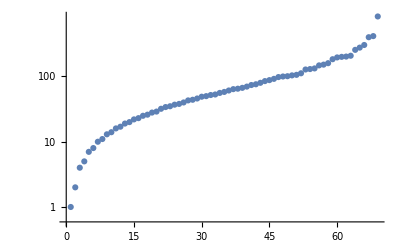

```mathematica
ListLogPlot[solutionsForCyle]
```

```mathematica
Map[Map[First,FactorInteger[#]]&,solutionsForCyle]//Flatten//Sort//DeleteDuplicates
```

{1,2,5,7,11,13,17,19,23,29,37,43,53,61,67,101,277}

```mathematica
Map[Map[First,FactorInteger[#]]&,Out[93]]//Flatten//Sort//DeleteDuplicates
```

{1,2,5,7,11,13,17,19,23,29,37,43,53,61,67,101,277}

```mathematica
Table[Prime[k],{k,40}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173}